## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="PGMd";
fitLabel="new_lma_1";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_PGMd";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/PGMd/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Null,Keq substrate}

{0.189,Keq value}

{3pg,Km or S05 substrate}

{0.0002,Km or S05 value}

{2pg,Km or S05 substrate}

{0.00019,Km or S05 value}

{{{3pg,Null},{23dpg,0.0001}},kcat substrates}

{330,kcat value}

{{{2pg,Null},{23dpg,0.0001}},kcat substrates}

{220,kcat value}

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
Get["MASSef`"];
```

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{(3pg)^c→0}

{(2pg)^c→0}

{(3pg)^c→1}

{(2pg)^c→1}

{}

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(23dpg)^c&(3pg)^c)_^-((PGMd^c&(23dpg)^c&(2pg)^c)_^)/K_PGMd4) Volume_c k_PGMd4^⟶}

Volume_c (-(PGMd^c&(23dpg)^c&(2pg)^c)_^ k_PGMd4^⟵+(PGMd^c&(23dpg)^c&(3pg)^c)_^ k_PGMd4^⟶)

1

2

3

0.03274

4

0.00023

5

0.000059

Simplifying...

6

0.038101

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fitLabel
```

new_lma_1

```mathematica
fitLabel="new_lma_3";
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/haldaneRatio_1.txt"	0.189
1	0.0001	0	0.00002	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateFor.txt"	626.7176791692085
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/absRateRev.txt"	417.8117861128057

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.04981505564
best_fit: 1.07544358347
best_fit: 1.08087762917
best_fit: 1.05273511286
best_fit: 1.07192076854
best_fit: 1.0131591662
best_fit: 1.098437855
best_fit: 1.06205116785
best_fit: 1.08598228439
best_fit: 1.09387959503
best_fit: 1.04563446064
best_fit: 1.04497973773
best_fit: 1.01747686267
best_fit: 1.09261370035
best_fit: 1.08154717652
best_fit: 1.04355718847
best_fit: 1.09760105082
best_fit: 1.09956627971
best_fit: 1.09129095923
best_fit: 0.965138313667
best_fit: 1.09772324464
best_fit: 1.09204940677
best_fit: 1.06066346177
best_fit: 1.09656845017
best_fit: 1.07651358963
best_fit: 1.06712652358
best_fit: 1.09486498932
best_fit: 1.0644719692
best_fit: 1.08405482588
best_fit: 1.07964755912
best_fit: 1.07324769925
best_fit: 0.968709326389
best_fit: 1.09338194471
best_fit: 1.0965218084
best_fit: 1.06207481282
best_fit: 1.05541439562
best_fit: 1.04776052112
best_fit: 1.01054007263
best_fit: 1.04025166407
best_fit: 1.06787177372
best_fit: 1.06334386215
best_fit: 0.996567134645
best_fit: 1.0924388261
best_fit: 0.995554911033
best_fit: 1.06462002837
best_fit: 1.09512161029
best_fit: 1.09851182737
best_fit: 1.09189411215
best_fit: 1.0853876514
best_fit: 1.08842257982
best_fit: 1.09113539701
best_fit: 1.06344344649
best_fit: 1.03502983609
best_fit: 1.07981706746
best_fit: 1.05623687926
best_fit: 1.07921533162
best_fit: 1.09829965622
best_fit: 1.07539277117
best_fit: 1.05247465377
best_fit: 1.09537528108
best_fit: 1.09695695558
best_fit: 0.9204665324
best_fit: 1.07432238844
best_fit: 1.08505934549
best_fit: 1.03879961158
best_fit: 1.03834709774
best_fit: 1.07215229674
best_fit: 0.9639116546
best_fit: 1.01092207897
best_fit: 1.09238225789
best_fit: 1.07546965671
best_fit: 1.09977956352
best_fit: 0.919619157502
best_fit: 1.03351268228
best_fit: 1.09608371423
best_fit: 0.945432074169
best_fit: 1.07593781454
best_fit: 0.932700772149
best_fit: 1.06962845826
best_fit: 1.025643126
best_fit: 1.06414060767
best_fit: 1.09322945907
best_fit: 1.09200453067
best_fit: 1.09928224581
best_fit: 1.04875140393
best_fit: 1.06226049877
best_fit: 1.06368235397
best_fit: 1.09664519755
best_fit: 1.0778071493
best_fit: 1.05275016231
best_fit: 1.09671915134
best_fit: 1.07877788236
best_fit: 1.0624189748
best_fit: 1.04744699225
best_fit: 1.07390736537
best_fit: 1.07966439737
best_fit: 1.09088677652
best_fit: 1.08048633678
best_fit: 1.04742426449
best_fit: 1.08752773936

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[lmaResultsFileName,1;;-5].

StringJoin::string: String expected at position 1 in StringTake[lmaResultsFileName,1;;-5]<>_2.txt.

Part::partd: Part specification /home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test_kcatKm_defs/input/TPI_general.dat⟦2⟧ is longer than depth of object.

```mathematica
dataFilePath
```

/home/mrama/Dropbox/MASSef/examples/PGMd/fit_PGMd/input/PGMd_new_lma_1.dat

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | haldaneRatio_1 | 0.0871358 | 0.00759265 | 0.0419924 | 22.2182 | 0.189 | 0.230992
1 | relRateFor_3pg | 0.204193 | 0.0416948 | 0.0341005 | 37.5105 | 0.0909091 | 0.0568086
1 | relRateFor_3pg | 0.195885 | 0.0383708 | 0.0496657 | 36.3035 | 0.136807 | 0.0871411
1 | relRateFor_3pg | 0.184037 | 0.0338695 | 0.0693463 | 34.5419 | 0.20076 | 0.131414
1 | relRateFor_3pg | 0.167969 | 0.0282136 | 0.0913321 | 32.0748 | 0.284747 | 0.193415
1 | relRateFor_3pg | 0.147597 | 0.0217849 | 0.111465 | 28.8126 | 0.386863 | 0.275398
1 | relRateFor_3pg | 0.123851 | 0.0153391 | 0.12406 | 24.8119 | 0.5 | 0.37594
1 | relRateFor_3pg | 0.0987314 | 0.00974789 | 0.12468 | 20.3348 | 0.613137 | 0.488457
1 | relRateFor_3pg | 0.0747394 | 0.00558598 | 0.113081 | 15.81 | 0.715253 | 0.602171
1 | relRateFor_3pg | 0.0539624 | 0.00291194 | 0.0933861 | 11.6844 | 0.79924 | 0.705854
1 | relRateFor_3pg | 0.0374468 | 0.00140226 | 0.0713098 | 8.26117 | 0.863193 | 0.791883
1 | relRateFor_3pg | 0.0251944 | 0.000634759 | 0.0512379 | 5.63617 | 0.909091 | 0.857853
1 | relRateRev_2pg | 0.340679 | 0.116062 | 0.108289 | 119.118 | 0.0909091 | 0.199199
1 | relRateRev_2pg | 0.315319 | 0.0994261 | 0.145959 | 106.69 | 0.136807 | 0.282766
1 | relRateRev_2pg | 0.282284 | 0.0796843 | 0.183798 | 91.5509 | 0.20076 | 0.384558
1 | relRateRev_2pg | 0.242398 | 0.058757 | 0.212827 | 74.7424 | 0.284747 | 0.497574
1 | relRateRev_2pg | 0.198372 | 0.0393516 | 0.22398 | 57.8964 | 0.386863 | 0.610843
1 | relRateRev_2pg | 0.1543 | 0.0238084 | 0.213296 | 42.6592 | 0.5 | 0.713296
1 | relRateRev_2pg | 0.11429 | 0.0130623 | 0.184578 | 30.1039 | 0.613137 | 0.797715
1 | relRateRev_2pg | 0.0810936 | 0.00657617 | 0.146838 | 20.5296 | 0.715253 | 0.862091
1 | relRateRev_2pg | 0.0555724 | 0.0030883 | 0.109103 | 13.6508 | 0.79924 | 0.908343
1 | relRateRev_2pg | 0.0370976 | 0.00137623 | 0.0769752 | 8.91749 | 0.863193 | 0.940168
1 | relRateRev_2pg | 0.0243069 | 0.000590826 | 0.0523315 | 5.75646 | 0.909091 | 0.961422
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateFor | 0.0871337 | 0.00759227 | 113.929 | 18.1787 | 626.718 | 512.789
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643
1 | absRateRev | 0.0871363 | 0.00759274 | 92.8308 | 22.2183 | 417.812 | 510.643

### Simulated Data and Best Fit Data Plot

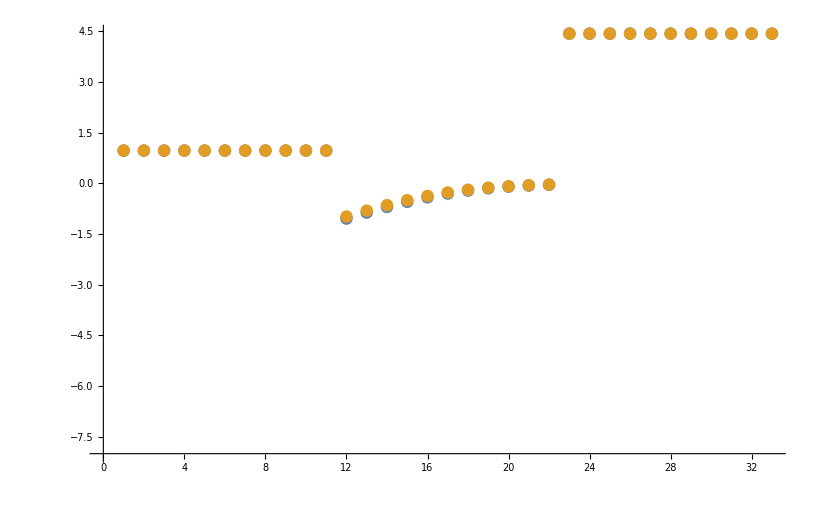

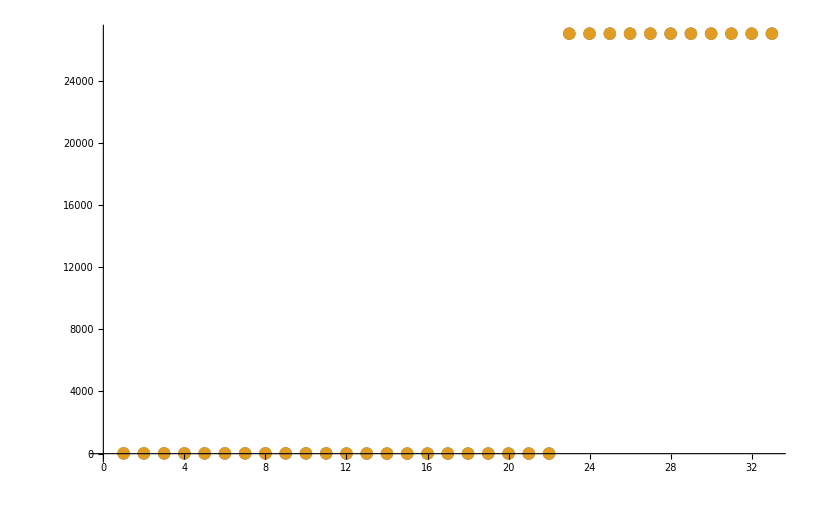

```mathematica
datasetI=40;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

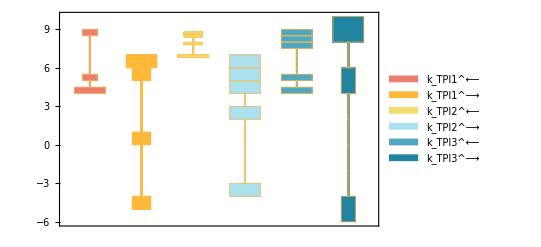

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

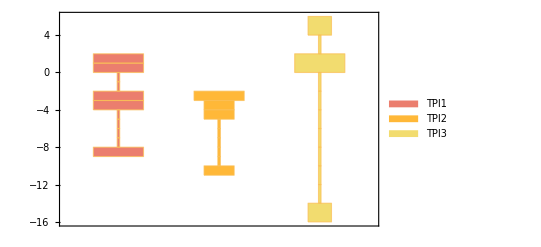

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

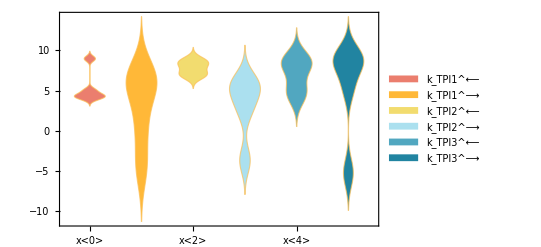

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1
assumedSaturatingConc=1
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]]
```

PGMd_total_Global→1

1

{k_PGMd1^⟵→0.0277271,k_PGMd1^⟶→13421.6,k_PGMd2^⟵→298072.,k_PGMd2^⟶→8.90642×10^8,k_PGMd3^⟵→2.4062×10^8,k_PGMd3^⟶→17528.1,k_PGMd4^⟵→512.491,k_PGMd4^⟶→543.873}

```mathematica
backCalculateKmsLocal[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

g3p^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→(k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟵ k_TPI3^⟵+k_TPI2^⟶ k_TPI3^⟶)/(2. k_TPI1^⟵ k_TPI2^⟶+k_TPI1^⟶ k_TPI2^⟶+2. k_TPI1^⟵ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟵+k_TPI1^⟶ k_TPI3^⟶+2. k_TPI2^⟶ k_TPI3^⟶)}}

{}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g3p^c→0.00103068}}

data value | predicted value | error in %
0.00103 | 0.00103068 | 0.0658914

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.000331956 | 65.9778
0.00019 | 0.0000763778 | 59.8011

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 512.789 | 18.1787
417.812 | 510.643 | 22.2183

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.189 | 0.230992 | 22.2182

```mathematica
dhapCoSubKm = {};
dhapCoSubKcat = {dhap^c->1};
relRatedhap=Values@FilterRules[fileListSub,inputPath<>"/relRateRev_dhap.txt"];
absRateRev=Values@FilterRules[fileListSub,inputPath<>"/absRateRev.txt"];
```

```mathematica
backCalulateKmSimple[relRate_,paramFitSub_,coSub_,substrate_]:=Block[{kmPredicted},

  kmPredicted = Solve[(relRate/.paramFitSub/. coSub)==0.5, substrate];
	kmPredicted = Flatten[Values @ kmPredicted];
  kmPredicted = If[Length[kmPredicted] > 1,
					Flatten[Select[kmPredicted, Head[#] === Real && #> 0  &]][[1]],
					kmPredicted
				];
Return[kmPredicted]
];
```

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
relRatedhap
```

{(dhap^c (k_TPI1^⟵ (k_TPI2^⟵+k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+k_TPI2^⟵ (k_TPI3^⟵+k_TPI3^⟶)))/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

#### Export rate back calculated parameter error distribution

```mathematica
kmList
```

{{1,3pg,0.0002,{0.000173,0.000227},{{23dpg,0.0001}},M,7,30,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}},{1,2pg,0.00019,{0.000155,0.000225},{{23dpg,0.0001}},M,7,30,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}}}

```mathematica
kcatList
```

{{1,{{3pg,Null},{23dpg,0.0001}},626.718,{605.827,647.608},1/s,7,37,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}},{1,{{2pg,Null},{23dpg,0.0001}},417.812,{393.123,442.501},1/s,7,37,{{trishcl,0.03}},{{mg2,0.005},{so4,0.005},{cl,0.02},{k,0.02}}}}

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;
rateConstList=Import[outputPath<>"/treated_data/rateconst_PGMd_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_3pg","Km_2pg","kcat_f","kcat_r","Keq"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kcatList[[1]][[3]], kcatList[[2]][[3]],KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];


predictedParamsList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,


{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_3pg","Km_2pg","kcat_f","kcat_r","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kcatList[[1]][[3]], kcatList[[2]][[3]],KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
backCalulateKmSimple[relRatedhap,paramFitSub,dhapCoSubKm,dhap^c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.268099}

```mathematica
absRateRev
```

{(dhap^c TPI_total_Global k_TPI1^⟵ k_TPI2^⟵ k_TPI3^⟵)/(k_TPI1^⟵ (k_TPI2^⟶+k_TPI3^⟵)+k_TPI2^⟶ k_TPI3^⟶+dhap^c k_TPI2^⟵ (k_TPI1^⟵+k_TPI3^⟵+k_TPI3^⟶))}

```mathematica
absRateRev /. paramFitSub /. dhapCoSubKcat /. enzymeSub
```

{16.5559}

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_g3p","kcat_f","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```